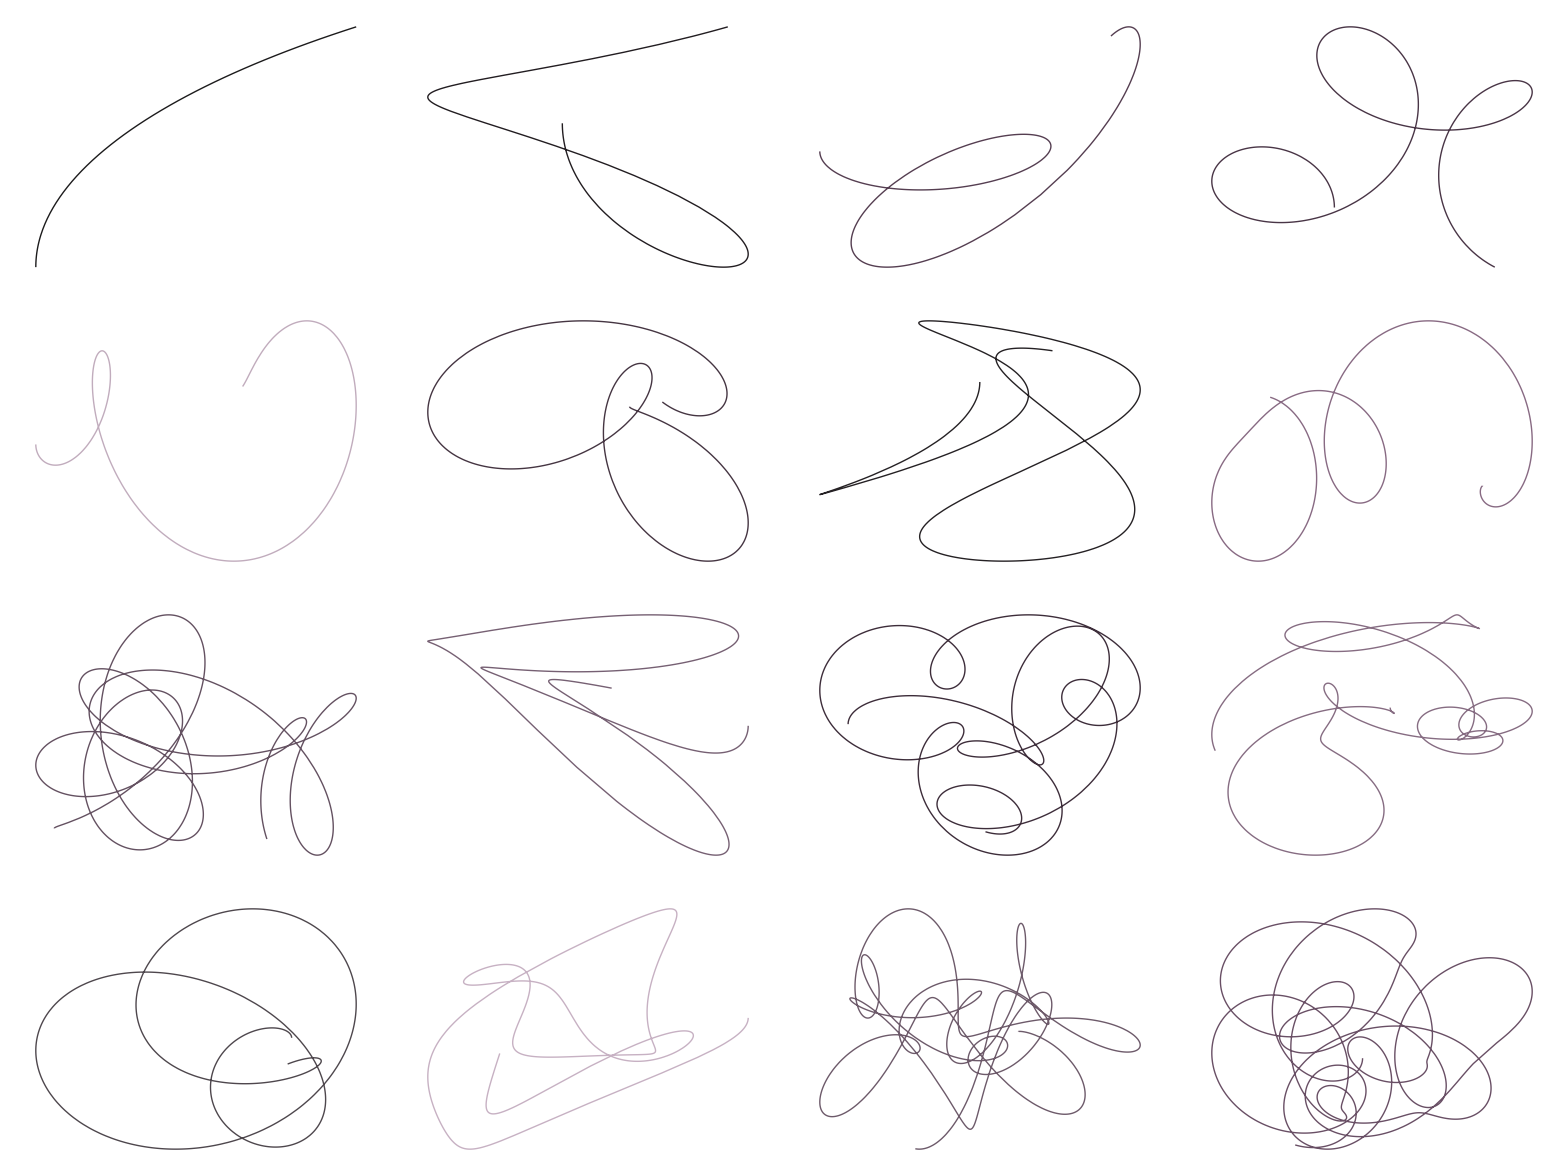

```mathematica
Grid[Partition[Table[Module[{f=Plus@@(#1Exp[I#2 t]&@@RandomVariate[NormalDistribution[],{2,10}])},
fxp=D[ComplexExpand[Re[f]],t];
fyp=D[ComplexExpand[Im[f]],t];
fxpp=D[ComplexExpand[Re[f]],t,t];
fypp=D[ComplexExpand[Im[f]],t,t];
curv=RealAbs[fxp fypp -fyp fxpp]/((fxp^2+fyp^2)^(3/2));
max=First@Quiet@FindMaximum[{curv,0≤t≤10},{t,5}];
min=First@Quiet@FindMinimum[{curv,0≤t≤10},{t,5}];
ParametricPlot[ReIm[f],{t,0,tf},Axes->False,PlotRange->All,ColorFunction->Function[{x,y,t},ColorData["FuchsiaTones"][Rescale[curv,{min,max}]]],ColorFunctionScaling->False,PlotStyle->Thick]],{tf,1,32,2}],4]]
```

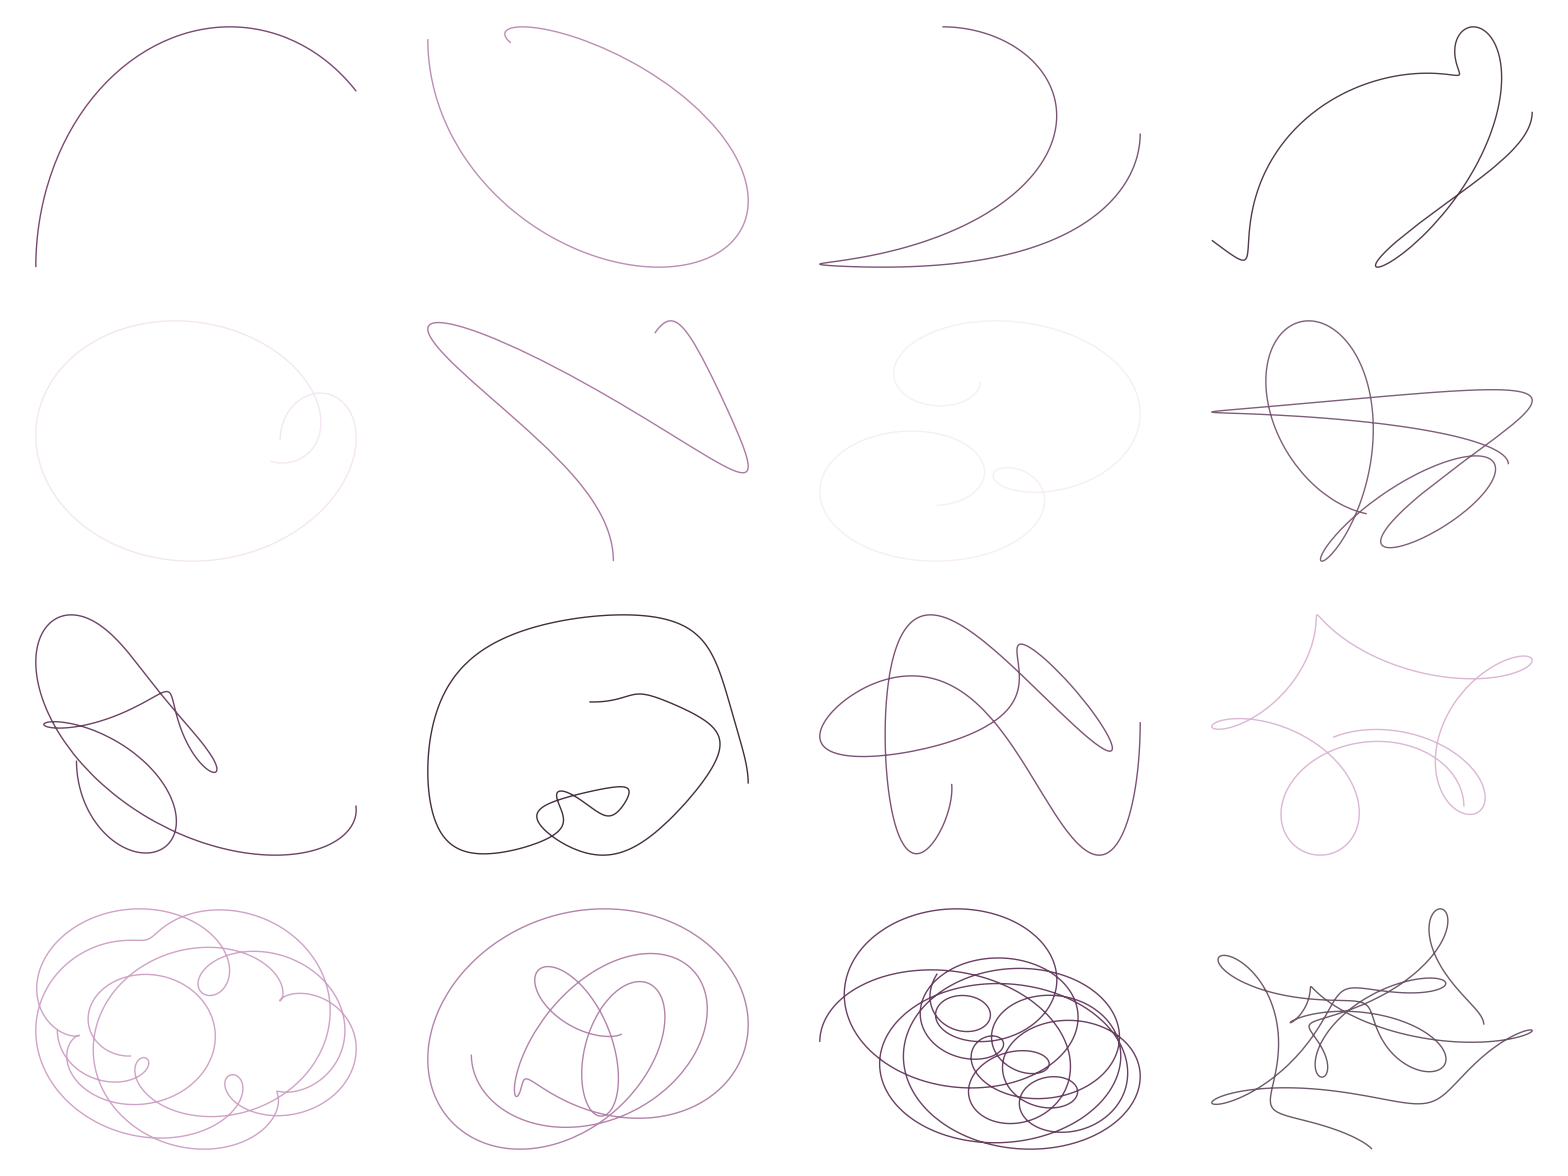

```mathematica
Grid[Partition[Table[Module[{f=Plus@@(#1Exp[I#2 t]&@@RandomVariate[NormalDistribution[],{2,10}])},
fxp=D[ComplexExpand[Re[f]],t];
fyp=D[ComplexExpand[Im[f]],t];
fxpp=D[ComplexExpand[Re[f]],t,t];
fypp=D[ComplexExpand[Im[f]],t,t];
curv=RealAbs[fxp fypp -fyp fxpp]/((fxp^2+fyp^2)^(3/2));
ParametricPlot[ReIm[f],{t,0,tf},Axes->False,PlotRange->All,ColorFunction->Function[{x,y,t},ColorData["FuchsiaTones"][curv]],PlotStyle->Thick]],{tf,1,32,2}],4]]
```

We all take curved, erratic, paths through life. However, what remains constant is that each experience is continuous from one moment to the next. The curves we take through life are dyed by how quickly our experiences change.

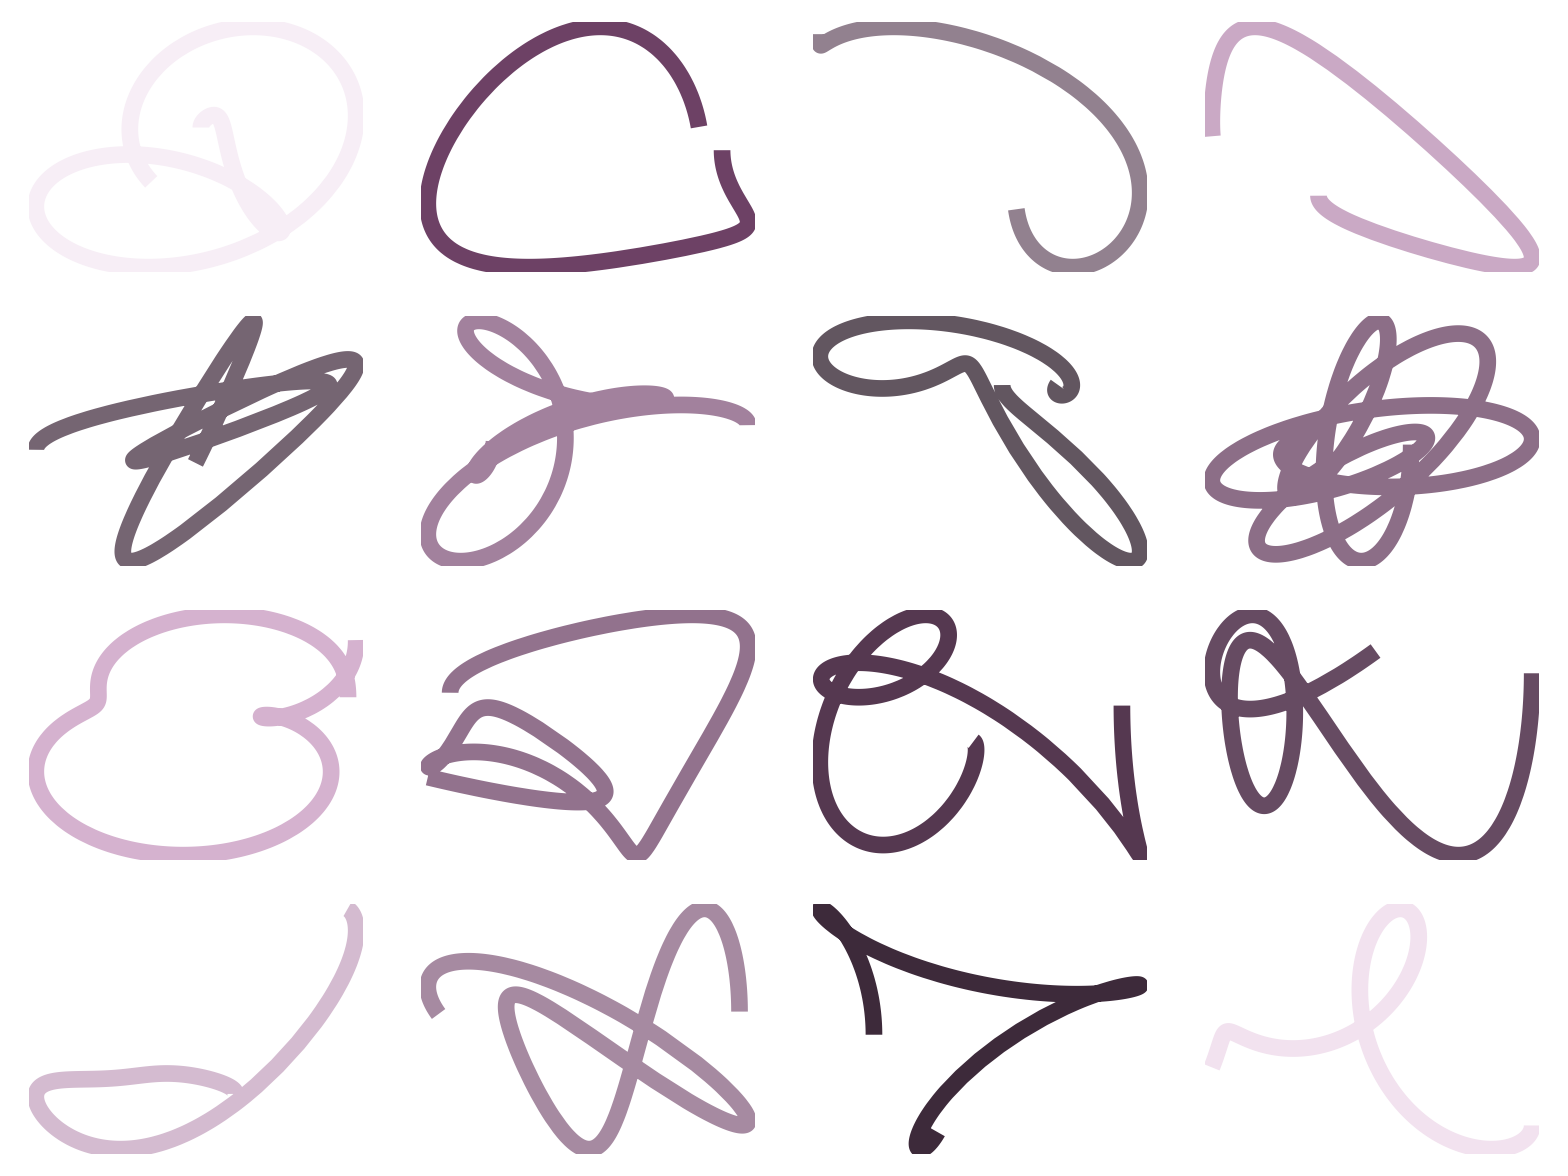

```mathematica
Grid[Partition[Table[Module[{f=Plus@@(#1Exp[I#2 t]&@@RandomVariate[NormalDistribution[],{2,10}])},
fxp=D[ComplexExpand[Re[f]],t];
fyp=D[ComplexExpand[Im[f]],t];
fxpp=D[ComplexExpand[Re[f]],t,t];
fypp=D[ComplexExpand[Im[f]],t,t];
curv=RealAbs[fxp fypp -fyp fxpp]/((fxp^2+fyp^2)^(3/2));
ParametricPlot[ReIm[f],{t,0,10},Axes->False,PlotRange->All,ColorFunction->Function[{x,y,t},ColorData["FuchsiaTones"][curv]],PlotStyle->Thickness[.03]]],16],4]]
```

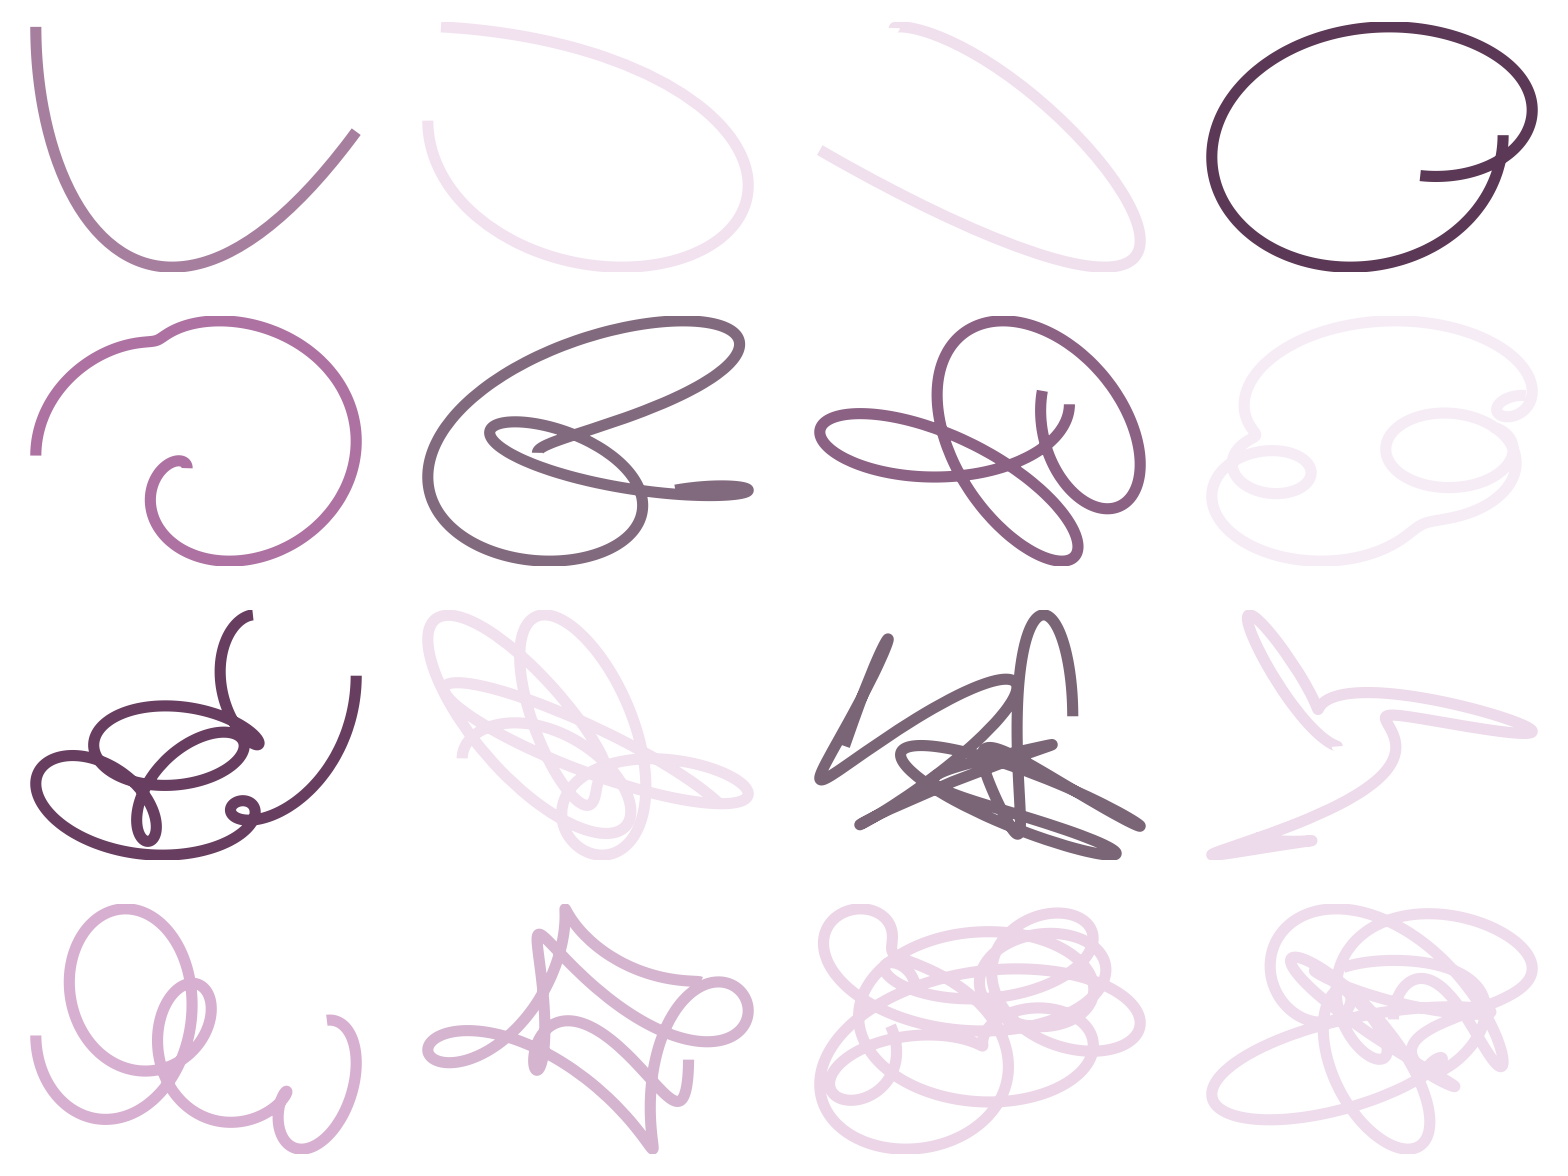

```mathematica
(*♡*)
Grid[Partition[Table[Module[{f=Plus@@(#1Exp[I#2 t]&@@RandomVariate[NormalDistribution[],{2,10}])},
fxp=D[ComplexExpand[Re[f]],t];
fyp=D[ComplexExpand[Im[f]],t];
fxpp=D[ComplexExpand[Re[f]],t,t];
fypp=D[ComplexExpand[Im[f]],t,t];
curv=RealAbs[fxp fypp -fyp fxpp]/((fxp^2+fyp^2)^(3/2));
ParametricPlot[ReIm[f],{t,0,tf},Axes->False,PlotRange->All,ColorFunction->Function[{x,y,t},ColorData["FuchsiaTones"][curv]],PlotStyle->Thickness[.02]]],{tf,1,32,2}],4]]
```

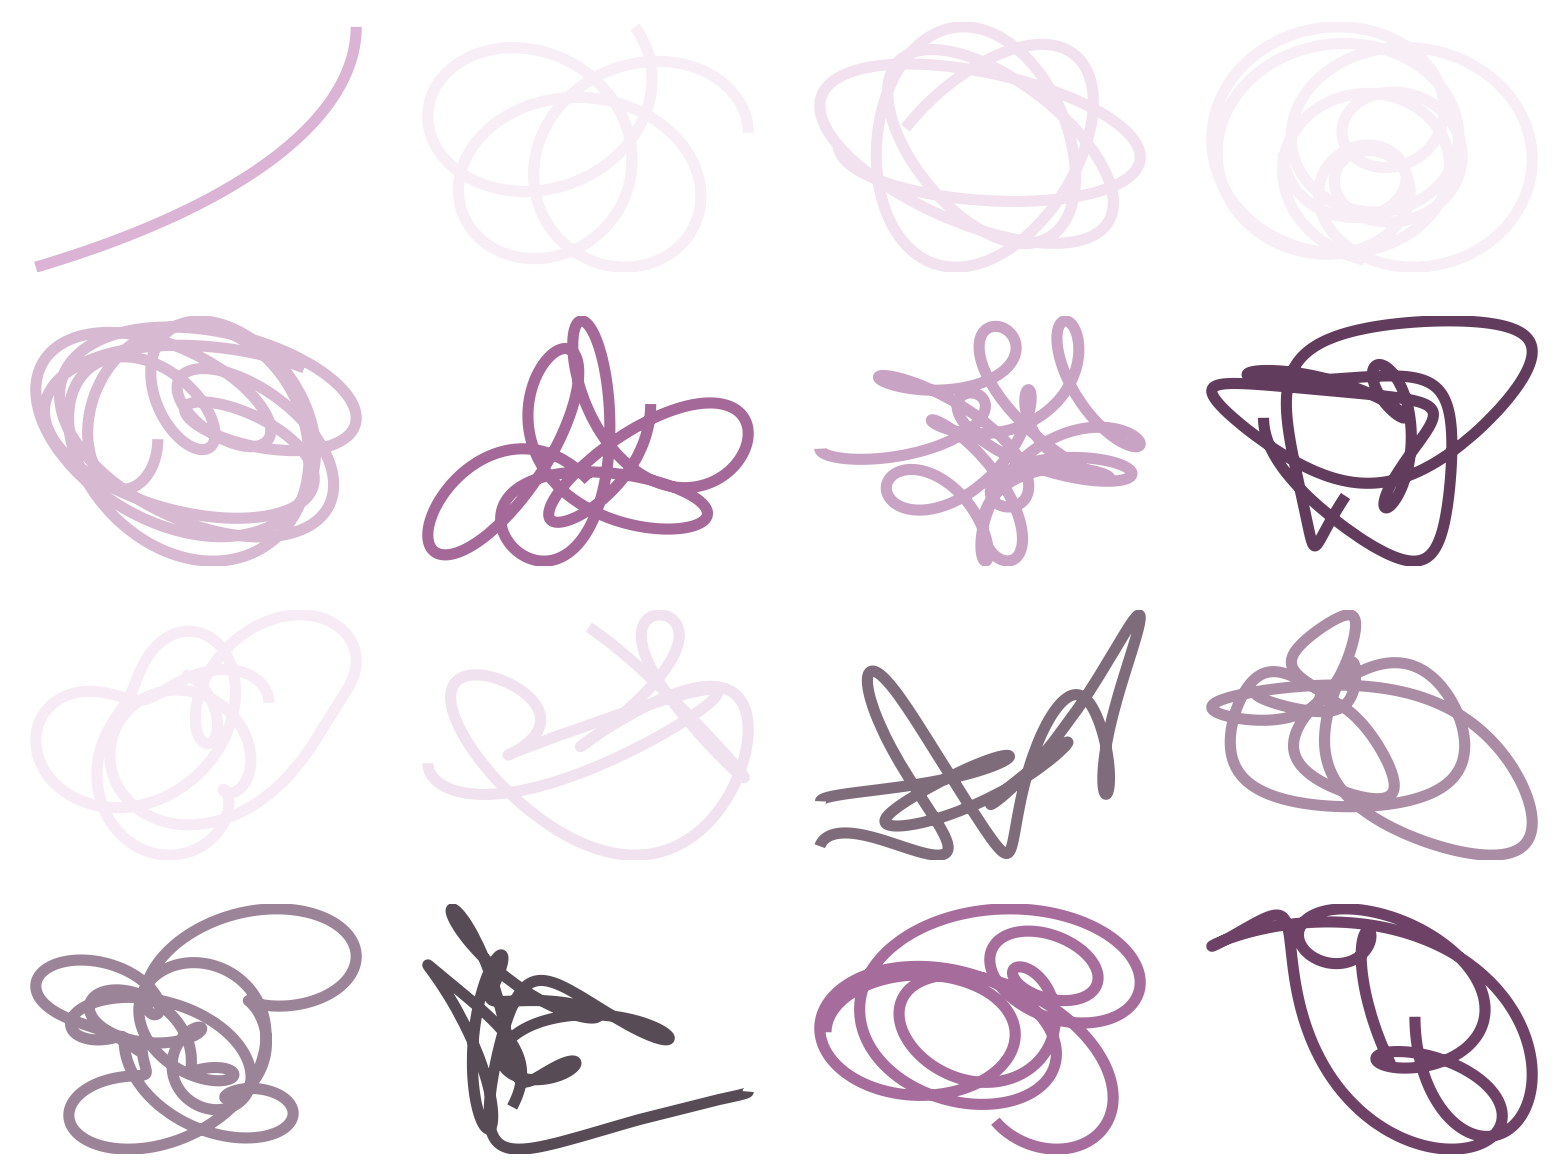

```mathematica
Grid[Partition[Table[Module[{f=Plus@@(#1Exp[I#2 t]&@@RandomVariate[NormalDistribution[],{2,l}])},
fxp=D[ComplexExpand[Re[f]],t];
fyp=D[ComplexExpand[Im[f]],t];
fxpp=D[ComplexExpand[Re[f]],t,t];
fypp=D[ComplexExpand[Im[f]],t,t];
curv=RealAbs[fxp fypp -fyp fxpp]/((fxp^2+fyp^2)^(3/2));
ParametricPlot[ReIm[f],{t,0,30},Axes->False,PlotRange->All,ColorFunction->Function[{x,y,t},ColorData["FuchsiaTones"][curv]],PlotStyle->Thickness[.02]]],{l,1,16}],4]]
```